```mathematica
SetDirectory[NotebookDirectory[]]
```

/data2/users/sanderson/Research/KLStats/Isochrone/NoErrors/PermutationMethod/HowManyStars

Frequencies as a function of the actions

```mathematica
Mtrue=12.2;
btrue=8.0;
OmegaR[Jr_,L_]:=Mtrue^2/(2(Jr+(L+Sqrt[L^2 + 4 Mtrue btrue])/2)^2)
OmegaTheta[Jr_,L_]:=(1+L/Sqrt[L^2+4 Mtrue btrue])/2 (Mtrue^2/(2(Jr+(L+Sqrt[L^2 + 4 Mtrue btrue])/2)^2))
```

Conversion factor between km/s and kpc/Myr

```mathematica
kmsTokpcMyr=0.001022729843472133;
```

Construct streams as clumps in (Jr, L, L_z) space

```mathematica
Ns=5;
sigmas=RandomReal[{0,.01},Ns]
inclinations=RandomVariate[UniformDistribution[{-π,π}],Ns]
```

{0.00812756,0.000522458,0.00814988,0.00265242,0.00788792}

{-2.7453,0.129781,-0.430806,2.31492,-1.4747}

```mathematica
spikyDist=MixtureDistribution[RandomReal[{0.1,1},Ns],Table[MultinormalDistribution[{RandomReal[{-1,1}],RandomReal[{2,10}],RandomReal[{0,10}]},DiagonalMatrix[{sigmas[[i]]/2,sigmas[[i]],sigmas[[i]]}]],{i,1,Ns}]]
```

MixtureDistribution[{0.245017,0.684757,0.54829,0.826421,0.903437},{MultinormalDistribution[{-0.78974,5.70343,0.355233},{{0.00406378,0.,0.},{0.,0.00812756,0.},{0.,0.,0.00812756}}],MultinormalDistribution[{-0.851258,4.35262,8.52056},{{0.000261229,0.,0.},{0.,0.000522458,0.},{0.,0.,0.000522458}}],MultinormalDistribution[{0.471009,7.90252,2.12692},{{0.00407494,0.,0.},{0.,0.00814988,0.},{0.,0.,0.00814988}}],MultinormalDistribution[{0.17649,3.70446,9.8486},{{0.00132621,0.,0.},{0.,0.00265242,0.},{0.,0.,0.00265242}}],MultinormalDistribution[{0.859839,9.95223,6.90041},{{0.00394396,0.,0.},{0.,0.00788792,0.},{0.,0.,0.00788792}}]}]

```mathematica
Nstars=30000;
```

```mathematica
Dimensions[trueJrL=RandomVariate[spikyDist,Nstars]]
```

{30000,3}

```mathematica
For[i=1,i≤Nstars,i++, While[(Abs[trueJrL[[i,1]]]>1)||(trueJrL[[i,3]]<0),trueJrL[[i]]=RandomVariate[spikyDist]]]
```

```mathematica
Dimensions[trueActions=Transpose[{trueJrL[[All,1]]*trueJrL[[All,2]],trueJrL[[All,2]],trueJrL[[All,3]]}]]
```

{30000,3}

### Clustering analysis picks out which points go to which stream so we can choose different inclinations for each COM orbit (θ_1 is a const of the motion)

```mathematica
Dimensions[streamIndex=ClusteringComponents[trueActions,Ns,1,Method->"Agglomerate"]]
```

{30000}

```mathematica
sel={};
For[i=1,i≤Ns,i++,AppendTo[sel,Thread[streamIndex==i]]];
```

```mathematica
Dimensions[sel]
```

{5,30000}

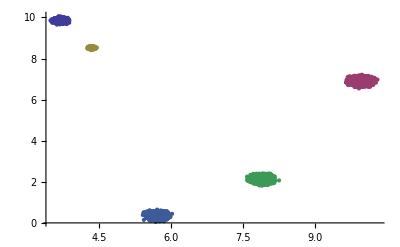

```mathematica
ListPlot[Table[Pick[trueJrL[[All,{2,3}]],sel[[i]]],{i,1,Ns}],PlotRange->All]
```

```mathematica
incs=Table[0,{i,1,Nstars}];

For[i=1,i≤Ns,i++,incs[[Flatten[Position[sel[[i]],True]]]]=RandomVariate[NormalDistribution[inclinations[[i]],2π/500],Length[Position[sel[[i]],True]]]];
```

```mathematica
Dimensions[incs]
```

{30000}

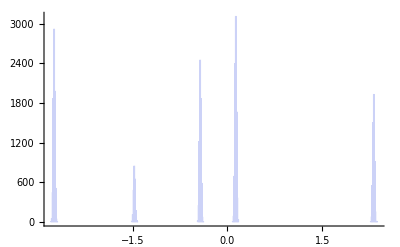

```mathematica
Histogram[incs,{-π,π,2π/500},PlotRange->All]
```

### Assign angles

```mathematica
Dimensions[initAngles=Transpose[{incs,Mod[RandomVariate[NormalDistribution[π/2,2π/500],Nstars],2π],Mod[RandomVariate[NormalDistribution[π/2,2π/500],Nstars],2π]}]]
```

{30000,3}

### Convert “initial” coordinates to configuration space (x,v) and measure satellite parameters

```mathematica
link=Install["/data2/users/sanderson/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math"]
```

LinkObject[/data2/users/sanderson/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math,543,15]

```mathematica
initCart=Table[{0,0,0,0,0,0},{i,1,Nstars}];
```

```mathematica
For[i=1, i≤Nstars, i++,initCart[[i]]=AAToCart[trueActions[[i]],initAngles[[i]]]]
```

```mathematica
Uninstall[link]
```

/data2/users/sanderson/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math

```mathematica
initPositions=initCart[[All,1;;3]];
initVelocities=initCart[[All,4;;6]]/kmsTokpcMyr;
```

```mathematica
ListPointPlot3D[initPositions,PlotRange->{{-50,50},{-50,50},{-50,50}}]
```

-Graphics3D-

```mathematica
iP=Table[Pick[initPositions,sel[[i]]],{i,1,Ns}];
```

```mathematica
ListPointPlot3D[iP,PlotRange->{{-50,50},{-50,50},{-50,50}}]
```

-Graphics3D-

```mathematica
iV=Table[Pick[initVelocities,sel[[i]]],{i,1,Ns}];
```

```mathematica
ListPointPlot3D[iV,PlotRange->All]
```

-Graphics3D-

```mathematica
meanX=Table[Mean[iP[[i]]],{i,1,Ns}]
```

{{21.22,-31.8923,40.6262},{-42.9164,33.0332,22.2317},{42.6606,17.6299,19.3381},{-10.2904,-19.3294,13.5346},{12.7478,-2.20995,2.63772}}

```mathematica
meanV=Table[Mean[iV[[i]]],{i,1,Ns}]
```

{{79.3243,-89.1859,216.664},{-236.122,-12.757,136.926},{229.868,10.0837,126.023},{104.668,-157.135,347.89},{71.0988,-357.15,279.216}}

```mathematica
dX=Table[Map[(#-meanX[[i]])&,iP[[i]]],{i,1,Ns}];
dV=Table[Map[(#-meanV[[i]])&,iV[[i]]],{i,1,Ns}];
```

```mathematica
sigX=Table[StandardDeviation[dX[[i]]],{i,1,Ns}]
```

{{1.45845,0.913738,0.616792},{2.77233,1.01508,4.944},{0.624279,0.878132,1.00669},{0.760363,0.81052,0.698229},{0.305454,0.562378,0.527644}}

```mathematica
Map[Norm,sigX]
```

{1.82823,5.75841,1.47454,1.31249,0.829446}

```mathematica
sigV=Table[StandardDeviation[dV[[i]]],{i,1,Ns}]
```

{{7.5351,4.28139,3.34667},{16.5797,5.2607,30.3901},{4.13717,4.6556,6.59338},{17.7802,18.7504,13.945},{8.83918,29.1146,39.1793}}

```mathematica
Map[Norm,sigV]
```

{9.29022,35.016,9.06992,29.3628,49.6065}

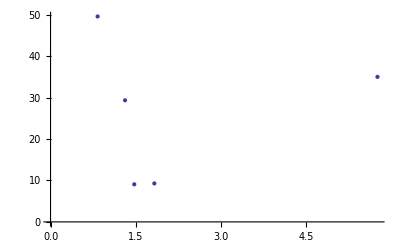

```mathematica
ListPlot[Transpose[{Map[Norm,sigX],Map[Norm,sigV]}]]
```

### Evolve angles forward in time using the frequencies

```mathematica
iA=Table[Pick[initAngles,sel[[i]]],{i,1,Ns}];

trueJrLi=Table[Pick[trueJrL,sel[[i]]],{i,1,Ns}];
```

```mathematica
iaCOM=Map[Mean,iA]
```

{{-2.74537,1.57119,1.57097},{0.129703,1.57091,1.57072},{-0.430604,1.57082,1.57087},{2.31468,1.5709,1.57083},{-1.47477,1.57105,1.57095}}

```mathematica
trueJrLCOM=Map[Mean,trueJrLi]
```

{{0.175988,3.70391,9.84835},{0.857905,9.95309,6.90062},{-0.851135,4.35304,8.52075},{0.47127,7.90067,2.12491},{-0.787684,5.70573,0.357439}}

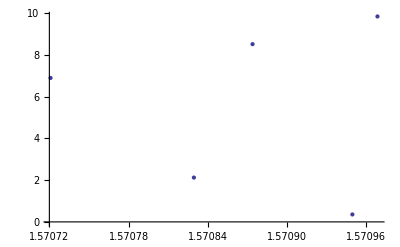

```mathematica
ListPlot[Transpose[{iaCOM[[All,3]],trueJrLCOM[[All,3]]}]]
```

#### For reference, orbital periods of stream COMs (in Myr)

```mathematica
OrbitalPds={2π/MapThread[OmegaTheta[#1,#2]&,{trueJrLCOM[[All,3]],trueJrLCOM[[All,2]]}],2π/MapThread[OmegaR[#1,#2]&,{trueJrLCOM[[All,3]],trueJrLCOM[[All,2]]}]}
```

{{67.4624,61.283,60.1974,34.404,24.0665},{39.9461,44.4265,36.5745,23.5887,15.3717}}

```mathematica
Transpose[OrbitalPds]//TableForm
```

67.4624 | 39.9461
61.283 | 44.4265
60.1974 | 36.5745
34.404 | 23.5887
24.0665 | 15.3717

#### Evolution time in Myr for each stream

```mathematica
eTimes=RandomReal[{500,5000},Ns]
```

{3143.44,2205.59,2421.9,4667.01,2011.57}

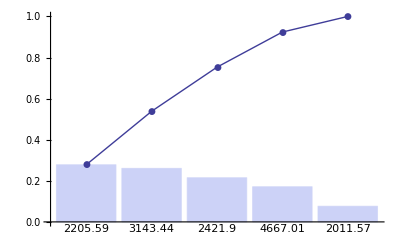

```mathematica
evolTime =eTimes[[streamIndex]];
<<StatisticalPlots`
ParetoPlot[evolTime]
```

#### Evolve the full streams forward in time

```mathematica
Dimensions[trueAngles=Transpose[{initAngles[[All,1]],Mod[initAngles[[All,2]]+Thread[OmegaTheta[trueJrL[[All,3]],trueJrL[[All,2]]]] evolTime,2π],Mod[initAngles[[All,3]]+Thread[OmegaR[trueJrL[[All,3]],trueJrL[[All,2]]]] evolTime,2π]}]]
```

{30000,3}

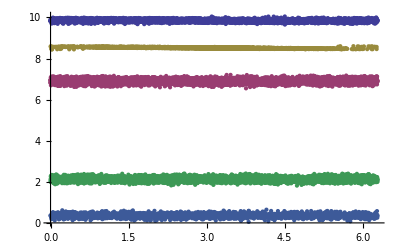

```mathematica
ListPlot[Table[Transpose[{Pick[trueAngles[[All,3]],sel[[i]]],Pick[trueJrL[[All,3]],sel[[i]]]}],{i,1,Ns}],PlotRange->{{0,2π},All}]
```

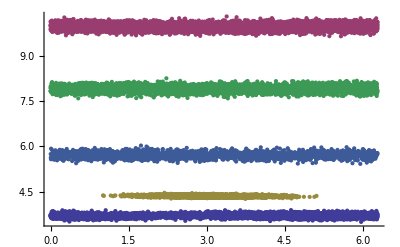

```mathematica
ListPlot[Table[Transpose[{Pick[trueAngles[[All,2]],sel[[i]]],Pick[trueJrL[[All,2]],sel[[i]]]}],{i,1,Ns}],PlotRange->{{0,2π},All}]
```

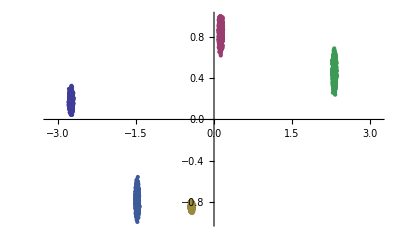

```mathematica
ListPlot[Table[Transpose[{Pick[trueAngles[[All,1]],sel[[i]]],Pick[trueJrL[[All,1]],sel[[i]]]}],{i,1,Ns}],PlotRange->{{-π,π},All}]
```

Convert coordinates to configuration space (x,v)

```mathematica
link=Install["/data2/users/sanderson/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math"]
```

LinkObject[/data2/users/sanderson/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math,544,15]

```mathematica
trueCart=Table[{0,0,0,0,0,0},{i,1,Nstars}];
```

```mathematica
For[i=1, i≤Nstars, i++,trueCart[[i]]=AAToCart[trueActions[[i]],trueAngles[[i]]]]
```

```mathematica
Uninstall[link]
```

/data2/users/sanderson/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math

```mathematica
truePositions=trueCart[[All,1;;3]];
trueVelocities=trueCart[[All,4;;6]]/kmsTokpcMyr;
```

```mathematica
tP=Table[Pick[truePositions,sel[[i]]],{i,1,Ns}];
tV=Table[Pick[trueVelocities,sel[[i]]],{i,1,Ns}];
```

```mathematica
ListPointPlot3D[tP]
```

-Graphics3D-

```mathematica
(*boxsize=30;*)
```

```mathematica
(*ColorData["Legacy","Panel"]*)
```

```mathematica
(*myYellow=ColorData["Legacy"]["CadmiumLemon"]*)
```

```mathematica
(*threeStreams=Show[ListPointPlot3D[{iP1,iP2,iP3},PlotStyle->{Lighter[Lighter[Red]],Lighter[Lighter[Green]],Lighter[Lighter[Blue]]},PlotRange->{{-boxsize,boxsize},{-boxsize,boxsize},{-boxsize,boxsize}}],Graphics3D[{Lighter[Red],Line[xCOM1],Lighter[Green],Line[xCOM2],Lighter[Blue],Line[xCOM3]}],ListPointPlot3D[{tP1,tP2,tP3},PlotStyle->{Darker[Red],Darker[Green],Darker[Blue]}],Graphics3D[{Cyan,Opacity[0.2],Sphere[{-8.5,0,0},10],(*Opacity[0.1],Sphere[{-8.5,0,0},25],*)Black,Opacity[1],Thickness[0.002],Line[{{-1,0,0},{1,0,0}}],Line[{{0,-1,0},{0,1,0}}],Line[{{0,0,-1},{0,0,1}}]}],Graphics3D[{Glow[myYellow],Black,Sphere[{-8.5,0,0},2]}],AspectRatio->1,AxesStyle->Directive[FontFamily->"Helvetica",FontSize->18],AxesLabel->{"x (kpc)","y (kpc)","z (kpc)"}]*)
```

```mathematica
Dimensions[dists=Map[Norm,Transpose[{truePositions[[All,1]]-8.0, truePositions[[All,2]],truePositions[[All,3]]}]]]
```

{30000}

```mathematica
{Min[dists],Max[dists]}
```

{1.27149,81.629}

```mathematica
(*Show[ListColorPlot[truePositions[[All,1]],truePositions[[All,3]],dists,.1,"Rainbow","x (kpc)","z (kpc)"],MyColorBar[{Min[dists],Max[dists]},5,"D"]]*)
```

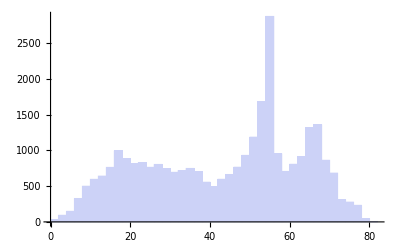

```mathematica
Histogram[dists,PlotRange->All]
```

```mathematica
DumpSave["streams5tot"<>ToString[Nstars]<>".mx",{truePositions,trueVelocities,trueCart,trueJrL,trueActions,trueAngles,s1sel,s2sel,s3sel,initAngles,Nstars,Ns}];
```